```mathematica
ClearAll["Global`*"];
```

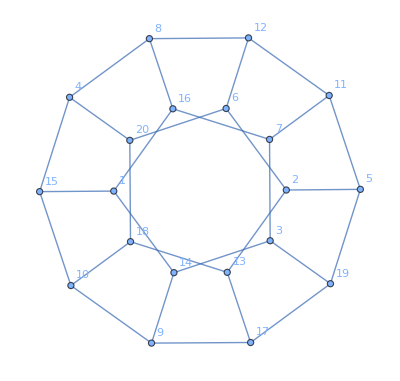

```mathematica
(* =========================1. Graph=========================*)bonds1Based={{1,14},{1,15},{1,16},{2,5},{2,6},{2,13},{3,7},{3,14},{3,19},{4,8},{4,15},{4,20},{5,11},{5,19},{6,12},{6,20},{7,11},{7,16},{8,12},{8,16},{9,10},{9,14},{9,17},{10,15},{10,18},{11,12},{13,17},{13,18},{17,19},{18,20}};

g=Graph[Range[12],UndirectedEdge@@@bonds1Based,VertexLabels->"Name"];

g(*optional to display*)
```

```mathematica
(* ====================2. Automorphism group====================*)
A=GraphAutomorphismGroup[g];
GroupOrder[A]        (*should be 120*)
```

120

```mathematica
(* ====================3. All group elements as lists====================*)(*Get all group elements as PermutationGroupElement/Cycles objects*)
elems=GroupElements[A];

(*Convert each element to a permutation list on {1,...,20} so that perm[[i]] is the image of i*)
elemsList=PermutationList[#,20]&/@elems;

Length[elemsList]    (*should be 120*)
```

120

```mathematica
(* ====================4. Basic permutation utilities====================*)

(*Composition:p∘q (apply q first,then p)*)
permCompose[p_List,q_List]:=p[[q]];

(*Inverse permutation*)
permInverse[p_List]:=Module[{inv=ConstantArray[0,Length[p]]},Do[inv[[p[[i]]]]=i,{i,Length[p]}];
inv];

(*Order of a permutation (small,so brute force is fine)*)
permOrder[p_List]:=Module[{e=Range[Length[p]],x=p,k=1},While[x=!=e,x=permCompose[p,x];
k++;];
k];
```

```mathematica
(* ====================5. Conjugacy classes (manual)====================*)conjugacyClasses=Module[{unseen=elemsList,classes={},rep,cls},While[unseen=!={},rep=First[unseen];
cls=Union[Table[Module[{h=elemsList[[k]],hinv},hinv=permInverse[h];
permCompose[h,permCompose[rep,hinv]]],{k,Length[elemsList]}]];
AppendTo[classes,cls];
unseen=Complement[unseen,cls];];
classes];

Length[conjugacyClasses]    (*should be 10*)
```

10

```mathematica
(* ====================6. Inspect sizes& orders====================*)classInfo=Table[<|"ClassIndex"->i,"Size"->Length[conjugacyClasses[[i]]],"OrderOfRepresentative"->permOrder[conjugacyClasses[[i,1]]],"Representative1Based"->conjugacyClasses[[i,1]]|>,{i,Length[conjugacyClasses]}];

classInfo

(*You should see sizes like {1,1,12,12,12,12,15,15,20,20} and orders 1,2,5,5,3,10,2,2,6,3 (up to reordering).*)
```

{<|ClassIndex→1,Size→1,OrderOfRepresentative→1,Representative1Based→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}|>,<|ClassIndex→2,Size→15,OrderOfRepresentative→2,Representative1Based→{1,2,4,3,6,5,8,7,10,9,12,11,14,13,15,16,18,17,20,19}|>,<|ClassIndex→3,Size→20,OrderOfRepresentative→3,Representative1Based→{1,2,8,9,6,16,4,10,7,3,18,20,15,13,14,5,12,19,11,17}|>,<|ClassIndex→4,Size→20,OrderOfRepresentative→6,Representative1Based→{2,1,11,20,15,14,12,18,17,19,8,4,5,16,6,13,7,10,3,9}|>,<|ClassIndex→5,Size→15,OrderOfRepresentative→2,Representative1Based→{2,1,12,19,15,13,11,17,18,20,7,3,6,16,5,14,8,9,4,10}|>,<|ClassIndex→6,Size→1,OrderOfRepresentative→2,Representative1Based→{2,1,18,17,14,13,20,19,12,11,10,9,6,5,16,15,4,3,8,7}|>,<|ClassIndex→7,Size→12,OrderOfRepresentative→5,Representative1Based→{3,18,5,1,6,4,11,15,19,9,12,8,17,13,7,20,2,14,16,10}|>,<|ClassIndex→8,Size→12,OrderOfRepresentative→5,Representative1Based→{3,18,15,19,4,20,1,9,11,5,14,10,7,17,13,6,8,16,12,2}|>,<|ClassIndex→9,Size→12,OrderOfRepresentative→10,Representative1Based→{5,14,12,19,4,10,6,16,7,3,18,20,11,17,2,1,8,9,15,13}|>,<|ClassIndex→10,Size→12,OrderOfRepresentative→10,Representative1Based→{11,10,17,8,9,14,3,15,2,6,13,1,5,12,7,20,19,4,16,18}|>}

```mathematica
(* ====================7. Convert to 0-based for Python====================*)
conjugacyClasses0Based=(#-1)&/@conjugacyClasses;

(*One example:show size and a sample permutation (0-based) per class*)
Table[<|"ClassIndex"->i,"Size"->Length[conjugacyClasses0Based[[i]]],"ExamplePerm0Based"->conjugacyClasses0Based[[i,1]]|>,{i,Length[conjugacyClasses0Based]}];
```

```mathematica
(* ====================8. Optional export====================*)(*Flat list of all 120 permutations in 0-based form*)(*Flat list of all 120 permutations (0-based)*)
allPerms0Based=Flatten[conjugacyClasses0Based,1];
(*Format each permutation as a Python-style list string*)
stringPerms="["<>StringRiffle[ToString/@#,", "]<>"]"&/@allPerms0Based;

Directory[]
(*Export each permutation on its own line*)
Export["C:\\Users\\camipolv\\Desktop\\ih_dodeca_permutations_0based.txt",stringPerms,"Lines"]
(*Grouped by classes (10 blocks),still 0-based*)
Export["C:\\Users\\camipolv\\Desktop\\ih_dodeca_conjugacy_classes_0based.m",conjugacyClasses0Based,"Table"];
```

C:\Users\camipolv

C:\Users\camipolv\Desktop\ih_dodeca_permutations_0based.txt